```mathematica
guneqn=Aaa 10^43 ((4 π)/3 r^3)^2(3 (Sin[ q r]-q r Cos[q r])/(q^3 r^3))^2;
Needs["PlotLegends`"]
```

#### One Scatterer

```mathematica
HeXeOneScattererSum=Flatten[Import["/Users/Max/ownCloud/Doktor/amoa1214/2D-Simulations/HeXe-one-scatterer-sum.dat","Table"]];
xVal=Table[N[(4π pixel)/(2.10 10^-5)],{pixel,1,1500}];
```

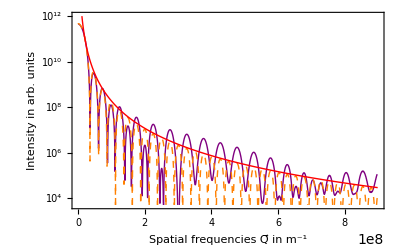

```mathematica
aa=ListLogPlot[{Transpose[{xVal,HeXeOneScattererSum^2}],Table[{q,guneqn}/.{r->125 10^-9,Aaa->0.7 10^9},{q,1,9 10^8,0.5 10^6}],Table[N[{q,Aa(2 π)/q^4}/.Aa->0.3 10^40],{q,1,9 10^8,10^6}]},Joined->True,
Frame->True,PlotStyle->{Directive[Purple,Thick],Directive[Dashed,Orange],Directive[{Red,Thick}]},FrameLabel->{"Spatial frequencies Q⃗ in m^-1","Intensity in arb. units"},FrameStyle->Directive[14],PlotLegend->{"One Xe-scatterer in He-droplet", "Scattering of sphere","∝ q^-4"},LegendPosition->{0.11,0.25},LegendShadow->None,LegendSize->{0.7,0.3},LegendTextSpace->7,
PlotRange->{{1,9 10^8},{0.5 10^4,0.01 10^14}}]
```

#### Few scatterer

```mathematica
HeXeIntactSum=Flatten[Import["/Users/Max/ownCloud/Doktor/amoa1214/2D-Simulations/HeXe-intact-sum.dat","Table"]];
```

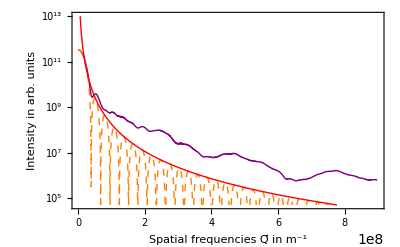

```mathematica
bb=ListLogPlot[{Transpose[{xVal,HeXeIntactSum^2}],Table[{q,guneqn}/.{r->113.588 10^-9,Aaa->0.9 10^9},{q,1,9 10^8,0.5 10^6}],Table[N[{q,Aa(2 π)/q^4}/.Aa->0.29 10^40],{q,1,9 10^8,10^6}]},Joined->True,
Frame->True,PlotStyle->{Directive[Purple,Thick],Directive[Dashed,Orange],Directive[{Red,Thick}]},FrameLabel->{"Spatial frequencies Q⃗ in m^-1","Intensity in arb. units"},FrameStyle->Directive[14],PlotLegend->{"Few Xe-scatterer in He-droplet", "Scattering of sphere","∝ q^-4"},LegendPosition->{0.11,0.25},LegendShadow->None,LegendSize->{0.7,0.3},LegendTextSpace->7,PlotRange->{{1,9 10^8},{5 10^4,0.1 10^14}}]
```

#### Many Random scatterer

```mathematica
HeXeIntactRandomSum=Flatten[Import["/Users/Max/ownCloud/Doktor/amoa1214/2D-Simulations/HeXe-intact-random-sum.dat","Table"]];
```

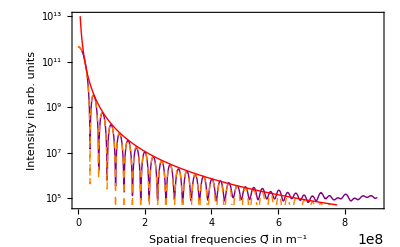

```mathematica
cc=ListLogPlot[{Transpose[{xVal,HeXeIntactRandomSum^2}],Table[{q,guneqn}/.{r->125 10^-9,Aaa->0.7 10^9},{q,1,9 10^8,0.5 10^6}],Table[N[{q,Aa(2 π)/q^4}/.Aa->0.29 10^40],{q,1,9 10^8,10^6}]},Joined->True,
Frame->True,PlotStyle->{Directive[Purple,Thick],Directive[Dashed,Orange],Directive[{Red,Thick}]},FrameLabel->{"Spatial frequencies Q⃗ in m^-1","Intensity in arb. units"},FrameStyle->Directive[14],PlotLegend->{"Many Xe-scatterer in He-droplet", "Scattering of sphere","∝ q^-4"},LegendPosition->{0.11,0.25},LegendShadow->None,LegendSize->{0.7,0.3},LegendTextSpace->7,PlotRange->{{1,9 10^8},{5 10^4,0.1 10^14}}]
```